# CSE 577 Instructor: Dianne Hansford Homework 2: Exploring Least Squares Approximation Due: March 1, 2016 by midnight Name : ANANT SRIVASTAVA ASU ID: 1209427008

Instructions on turning in your homework:
-- Name your notebook lastname_firstname_hw2.nb
-- Submit it via the course Blackboard site. 
-- Be sure to include comments/text describing your work. This will make it possible to receive partial credit.

The purpose of this homework is to explore least squares “lsq” approximation with Bezier curves.  
Create a subroutine to set up and solve the least squares problem. You must set up the normal equations yourself, but you can use LinearSolve.
You should make each plot attractive and easy to interpret by using colors, a variety of point sizes and line width, and labels.
 

Part 1:
Think of your favorite publically traded company and use “FinancialData” to get the stock price data over each day of january 2016. (Example: GE is General Electric.) 
Fit a lsq line to identify a trend of this stock price. Plot the stock price data and the lsq line. Label the plot to let the reader know what they are seeing -- company, time period, etc.
Hint: Data can be  organized as (i, price on day i) for i=1,2,.... (See ListPlot) No need to label the plot with the actual dates.
Here is an example for GE. You will need to extract the stock price data. (Don’t use GE for your data set.)

data = (4 | 54.4093
5 | 54.6576
6 | 53.6647
7 | 51.7981
8 | 51.957
11 | 51.9272
12 | 52.4037
13 | 51.2719
14 | 52.7314
15 | 50.6265
19 | 50.1996
20 | 50.4279
21 | 50.1201
22 | 51.9172
25 | 51.4208
26 | 51.7981
27 | 50.8549
28 | 51.6889
29 | 54.6973)knot = (0.
0.0555556
0.111111
0.166667
0.222222
0.277778
0.333333
0.388889
0.444444
0.5
0.555556
0.611111
0.666667
0.722222
0.777778
0.833333
0.888889
0.944444
1.)

vandermont matrix = (1 | 0
0.944444 | 0.0555556
0.888889 | 0.111111
0.833333 | 0.166667
0.777778 | 0.222222
0.722222 | 0.277778
0.666667 | 0.333333
0.611111 | 0.388889
0.555556 | 0.444444
0.5 | 0.5
0.444444 | 0.555556
0.388889 | 0.611111
0.333333 | 0.666667
0.277778 | 0.722222
0.222222 | 0.777778
0.166667 | 0.833333
0.111111 | 0.888889
0.0555556 | 0.944444
0 | 1)rhs = (4 | 54.4093
5 | 54.6576
6 | 53.6647
7 | 51.7981
8 | 51.957
11 | 51.9272
12 | 52.4037
13 | 51.2719
14 | 52.7314
15 | 50.6265
19 | 50.1996
20 | 50.4279
21 | 50.1201
22 | 51.9172
25 | 51.4208
26 | 51.7981
27 | 50.8549
28 | 51.6889
29 | 54.6973)

bezier points = (3.07895 | 52.8925
29.7632 | 51.1677)

First data points = {4,54.4093}  Last data = {29,54.6973}

explicit matrix = (4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
11 | 1
12 | 1
13 | 1
14 | 1
15 | 1
19 | 1
20 | 1
21 | 1
22 | 1
25 | 1
26 | 1
27 | 1
28 | 1
29 | 1)  rhs = (54.4093
54.6576
53.6647
51.7981
51.957
51.9272
52.4037
51.2719
52.7314
50.6265
50.1996
50.4279
50.1201
51.9172
51.4208
51.7981
50.8549
51.6889
54.6973)

ab = {-0.0650307,53.098}

Endpoints: p1={4,52.8379}  p2 = {29,51.2121}

line points = (3.07895 | 52.8925
4.5614 | 52.7967
6.04386 | 52.7009
7.52632 | 52.605
9.00877 | 52.5092
10.4912 | 52.4134
11.9737 | 52.3176
13.4561 | 52.2218
14.9386 | 52.1259
16.4211 | 52.0301
17.9035 | 51.9343
19.386 | 51.8385
20.8684 | 51.7427
22.3509 | 51.6468
23.8333 | 51.551
25.3158 | 51.4552
26.7982 | 51.3594
28.2807 | 51.2635
29.7632 | 51.1677)

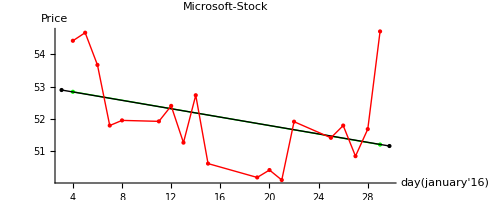

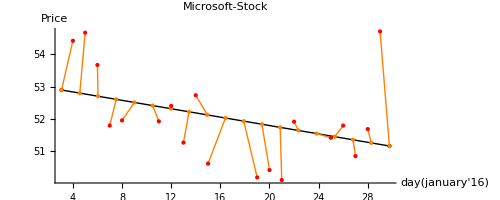

```mathematica
(*Setting up data as {day number, stock price *)
data1 = FinancialData["NASDAQ:MSFT","Price",{{2016,1,1},{2016,1,29}}];
m1= Length[data1] -1;
data = Table[{data1[[i,1]][[3]],data1[[i,2]]},{i,1,m1+1}];

(*setting knot points for unform parameerization and calculating the corrosponding degree beizer points*)
knot=Table[t,{t,0.0,1.0,1/m1}];
Print["data = ",MatrixForm[data],"knot = ",MatrixForm[knot]];
n = 1; (* degree 1 *)
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m1+1},{j,1,n+1}];
Print["vandermont matrix = ",MatrixForm[vandermonde],"rhs = ",MatrixForm[data]];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data];
Print["bezier points = ",MatrixForm[bez]];
Print["First data points = ",data[[1]],"  Last data = ",data[[m1+1]]];

(*setting explicit line form to get the endpoints*)
explicit = Table[{data[[i,1]], 1},{i,1,m1+1}];
tdata = Transpose[data];
ab=LinearSolve[Transpose[explicit].explicit,Transpose[explicit].tdata[[2]]];
p1 = {data[[1,1]],ab[[1]]*data[[1,1]] + ab[[2]]};
p2 = {data[[m1+1,1]],ab[[1]]*data[[m1+1,1]] + ab[[2]]};
Print["explicit matrix = ",MatrixForm[explicit], "  rhs = ",MatrixForm[tdata[[2]]]];
Print["ab = ",ab];
Print["Endpoints: p1=",p1,"  p2 = ",p2];

linepts = Table[(1-knot[[i]])*bez[[1]] + knot[[i]]*bez[[2]],{i,1,m1+1}];
Print["line points = ", MatrixForm[linepts]];

(*Plotting results*)
dplot=ListPlot[data, PlotStyle->{Red,PointSize[Medium]},PlotLabel->Style["Microsoft-Stock",FontSize->18],AxesLabel->{"day(january'16)",Price},LabelStyle->Directive[Blue]];
dpolyplot = ListLinePlot[data, PlotStyle->{Red,Thin},PlotRange->Automatic];
lineparams = Graphics[{PointSize[Medium],Orange,Point[linepts]}];
paraerrsplot = Table[Graphics[{PointSize[Medium],Orange,Line[{linepts[[i]],data[[i]]}]}],{i,1,m1+1}];
bezpolyplot=Graphics[ListLinePlot[bez, PlotStyle->{Black,Thin}]];
bezpointsplot=Graphics[{Black,PointSize[Large],Point[bez]},Axes->True,PlotLabel->Style["Microsoft-Stock",FontSize->18],AxesLabel->{"day(january'16)",Price}];
exppointsplot =Graphics[{Green,PointSize[Large],Point[{p1,p2}]},Axes->True,PlotLabel->Style["Microsoft-Stock",FontSize->18],AxesLabel->{"day(january'16)",Price}];
exppolyplot=ListLinePlot[{p1,p2}, PlotStyle->{Green,Thick}];

Show[{exppointsplot,exppolyplot,bezpointsplot,bezpolyplot,dplot, dpolyplot}]
Show[{bezpointsplot,bezpolyplot,lineparams,paraerrsplot,dplot}]
```

```mathematica
Test for uniform and chord length Parameterization, given dataset  data4, printing data, Chord Lenght parameters and Uniform Length parameters.
```

```mathematica
(*chord length parameterization; t=m*)
crp[t_,knot1_,data_]:=Module[{knot =knot1,d=data},
For[k=1,k≤t,k++,
If[k==1,
knot[[k]]=0,
knot[[k]]= knot[[k-1]]+ Norm[d[[k]]-d[[k-1]]];
]
];
knot
];
data4=Table[{t,Cos[t]},{t,0.0,10.0}];
m2 = Length[data4] -1;
data = data4;
(*Chord length parameterization and normalization*)
knot1 = Table[t,{t,1,m1+1}];
knot1 = crp[m2+1,knot1,data];
div = knot1[[m2+1]]-knot1[[1]];
normal = Table[knot1[[t]]/div-knot1[[1]]/div,{t,1,m2+1}];

(*Uniform Length Length Prameterization*)
knot2=Table[t,{t,0.0,1.0,1/m2}];
Print["data = ",MatrixForm[data]];
Print["Chord Length = "MatrixForm[normal],"Uniform Length",MatrixForm[knot2]];
```

data = (0. | 1.
1. | 0.540302
2. | -0.416147
3. | -0.989992
4. | -0.653644
5. | 0.283662
6. | 0.96017
7. | 0.753902
8. | -0.1455
9. | -0.91113
10. | -0.839072)

Chord Length =  (0.
0.0925003
0.208799
0.305699
0.394371
0.509563
0.611034
0.696849
0.809887
0.915737
1.)Uniform Length(0.
0.1
0.2
0.3
0.4
0.5
0.6
0.7
0.8
0.9
1.)

Part 2
Compare uniform versus chord length parametrization. 
Using the data set “data2” below, find the degree 5 approximate for each parametrization. Compute the least squares error of each approximation and report the results as a label in the plot of the data and approximation. Print the first ten parameter values for each parametrization.
Repeat this experiment with your own data set. Create an interesting noisy data set with 100 points. The data set must be such that the uniform and chord length parametrization are different. .

Part 2 Experiment 1

Chord Lendth Parameters =  (0.
0.129011
0.246586
0.3521
0.465274
0.570837
0.677222
0.785221
0.889496
1.)Uniform Length Parameters =  (0.
0.111111
0.222222
0.333333
0.444444
0.555556
0.666667
0.777778
0.888889
1.)

bezier points = (0.00112724 | 0.280762
1.51285 | 2.09051
3.99556 | 1.45762
5.64923 | 3.37771
8.04971 | 2.61762
10.0013 | 3.4809)

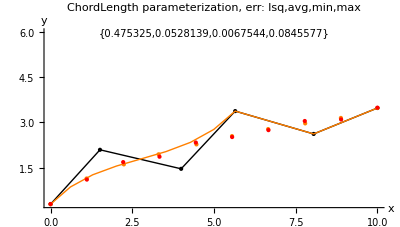

bezier points = (-1.57543×10^-15 | 0.279925
2. | 2.39696
4. | 1.24402
6. | 3.59703
8. | 2.55393
10. | 3.48214)

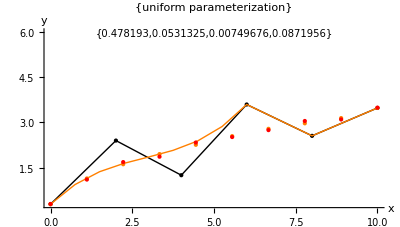

Part 2 Experiment 2

Chord Lendth Parameters =  (0.
0.00103082
0.00153926
0.00209069
0.00307876
0.00499225
0.00772178
0.00988729
0.0109907
0.014172)Uniform Length Parameters =  (0.
0.010101
0.020202
0.030303
0.040404
0.0505051
0.0606061
0.0707071
0.0808081
0.0909091)

bezier points = (3.98384 | 6.11691
76.6491 | 56.7784
30.9361 | 85.4036
106.837 | 21.4601
81.7598 | 140.229
100.098 | 82.0973)

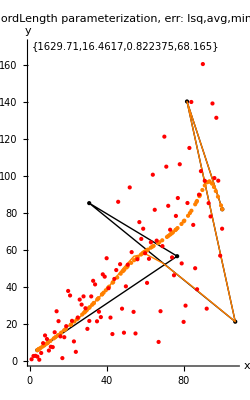

bezier points = (1. | 2.20675
20.8 | 15.1348
40.6 | 56.082
60.4 | 34.2092
80.2 | 95.5893
100. | 91.5034)

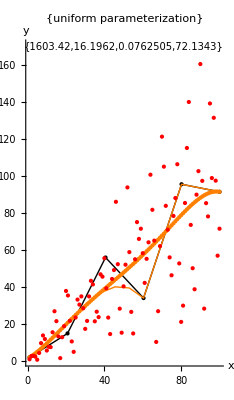

```mathematica
(*Part 2 Experiment 1 *)
(*Least square error returns lsq error, average error, Minimum and Maximum error*)
lsqerr[data_,knot_,bez_,m_,n_]:=Module[{lsq =0,avg =0,d =0,max=-1,min=10^10},
v=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
list = v.bez;
For[i=1,i≤m,i++,
d =Norm[list[[i]]-data[[i]]];
If[d>max,max = d];
If[d<min,min = d];
lsq = lsq+d;
];
avg = lsq/m;
{lsq,avg,min,max}
];

Print["Part 2 Experiment 1"];
m = 9;
data2=Table[{t,Sqrt[t]+0.4RandomReal[]},{t,0.0,10.0,10/m}];
m = Length[data2] -1;
data = data2;

(*Chord length parameterization and normalization*)
knot1 = crp[m+1,knot1,data];
div = knot1[[m+1]]-knot1[[1]];
normal = Table[knot1[[t]]/div-knot1[[1]]/div,{t,1,m+1}];

(*Uniform Length Length Prameterization*)
knot2=Table[t,{t,0.0,1.0,1/m}];

Print["Chord Lendth Parameters = "MatrixForm[normal],"Uniform Length Parameters = "MatrixForm[knot2]];

(*Chord length procedure and plotting *)
knot = normal;
n = 5; (* degree 5 *)
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data];
Print["bezier points = ",MatrixForm[bez]];

linepts = vandermonde.bez;
dplot=ListPlot[data, PlotStyle->{Red,PointSize[Medium]}];
dpolyplot = ListLinePlot[data, PlotStyle->{Red,Thin},PlotRange->Automatic];
lineparams = Graphics[{PointSize[Medium],Orange,Point[linepts]}];
paraerrsplot = Graphics[{PointSize[Medium],Orange,BezierCurve[bez,SplineDegree->n],Text[Style[lsqerr[data,knot,bez,m,n],FontSize->10,Black],{5,6}]}];
bezpolyplot=Graphics[ListLinePlot[bez, PlotStyle->{Black,Thin}]];
bezpointsplot=Graphics[{Black,PointSize[Large],Point[bez]},Axes->True,AxesLabel->{x,y},PlotLabel->"ChordLength parameterization, err: lsq,avg,min,max"];
lsqerr[data,knot,bez,m,n];
Show[{bezpointsplot,bezpolyplot,lineparams,paraerrsplot,dplot}]

(*Uniform length procedure and plotting *)
knot = knot2;
n = 5; (* degree 5 *)
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data];
Print["bezier points = ",MatrixForm[bez]];

linepts = vandermonde.bez;
dplot=ListPlot[data, PlotStyle->{Red,PointSize[Medium]}];
dpolyplot = ListLinePlot[data, PlotStyle->{Red,Thin},PlotRange->Automatic];
lineparams = Graphics[{PointSize[Medium],Orange,Point[linepts]}];
paraerrsplot = Graphics[{PointSize[Medium],Orange,BezierCurve[bez,SplineDegree->n],Text[Style[lsqerr[data,knot,bez,m,n],FontSize->10,Black],{5,6}]}];
bezpolyplot=Graphics[ListLinePlot[bez, PlotStyle->{Black,Thin}]];
bezpointsplot=Graphics[{Black,PointSize[Large],Point[bez]},Axes->True,AxesLabel->{x,y},PlotLabel->{"uniform parameterization"}];

Show[{bezpointsplot,bezpolyplot,lineparams,paraerrsplot,dplot}]

Print["Part 2 Experiment 2"];
(*Part 2 Experiment 1 *)

data3=Table[{t,t+t*RandomReal[]*Sin[t]},{t,1,100,1}];
m = Length[data3] -1;
data = data3;

(*Uniform Length Length Prameterization*)
knot2=Table[t,{t,0.0,1.0,1/m}];

(*Chord length parameterization and normalization*)
knot1 = crp[m+1,knot2,data];
div = knot1[[m+1]]-knot1[[1]];
normal = Table[knot1[[t]]/div-knot1[[1]]/div,{t,1,m+1}];

(* First ten values of length parameters*)
Print["Chord Lendth Parameters = "MatrixForm[normal[[1;;10]]],"Uniform Length Parameters = "MatrixForm[knot2[[1;;10]]]];
knot = normal;
n = 5; (* degree 5 *)
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data];
Print["bezier points = ",MatrixForm[bez]];

linepts = vandermonde.bez;
dplot=ListPlot[data, PlotStyle->{Red,PointSize[Small]}];
dpolyplot = ListLinePlot[data, PlotStyle->{Red,Thin},PlotRange->Automatic];
lineparams = Graphics[{PointSize[Small],Orange,Point[linepts]}];
paraerrsplot = Graphics[{PointSize[Medium],Orange,BezierCurve[bez,SplineDegree->n],Text[Style[lsqerr[data,knot,bez,m,n],FontSize->10,Black],{50,170}]}];
bezpolyplot=Graphics[ListLinePlot[bez, PlotStyle->{Black,Thin}]];
bezpointsplot=Graphics[{Black,PointSize[Medium],Point[bez]},Axes->True,AxesLabel->{x,y},PlotLabel->"ChordLength parameterization, err: lsq,avg,min,max"];
Show[{bezpointsplot,bezpolyplot,lineparams,paraerrsplot,dplot}]

(*Uniform length procedure and plotting *)
knot = knot2;
n = 5; (* degree 5 *)
vandermonde=Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data];
Print["bezier points = ",MatrixForm[bez]];

linepts = vandermonde.bez;
dplot=ListPlot[data, PlotStyle->{Red,PointSize[Small]}];
dpolyplot = ListLinePlot[data, PlotStyle->{Red,Thin},PlotRange->Automatic];
lineparams = Graphics[{PointSize[Small],Orange,Point[linepts]}];
paraerrsplot = Graphics[{PointSize[Medium],Orange,BezierCurve[bez,SplineDegree->n],Text[Style[lsqerr[data,knot,bez,m,n],FontSize->10,Black],{50,170}]}];
bezpolyplot=Graphics[ListLinePlot[bez, PlotStyle->{Black,Thin}]];
bezpointsplot=Graphics[{Black,PointSize[Large],Point[bez]},Axes->True,AxesLabel->{x,y},PlotLabel->{"uniform parameterization"}];

Show[{bezpointsplot,bezpolyplot,lineparams,paraerrsplot,dplot}]
```

Part 3
Create an interesting functional data set with 100 points.Using Manipulate, let the 50th point move vertically, becoming an outlier. Display the points, approximation, and least squares error.

```mathematica
(*Fitting data; y = y coordinate for manipulate*)
fit[y_,data_]:=Module[{d=data},d[[50,2]]= y;d];

(*dynamic bezire points calculation*)
bezd[y_,v_,data_]:= Module[{b,d=data,x=y},b= LinearSolve[Transpose[v].v,Transpose[v].fit[x,d]];b];

(*A partial noisy data set *)
data5=Table[{t,t+7*Random[]},{t,1,100}];
m = Length[data5] -1;
(*degree 1*)
knot=Table[t,{t,0,1,1/m}];
vandermonde=Table[BernsteinBasis[1,j-1,knot[[i]]],{i,1,m+1},{j,1,2}];
bez=LinearSolve[Transpose[vandermonde].vandermonde,Transpose[vandermonde].data5];
linepts = vandermonde.bez;

Manipulate[Show[
ListPlot[fit[y,data5],PlotLabel->{"Least Square Error = ", lsqerr[data5,knot,bezd[y,vandermonde,data5],m,1]}],
ListLinePlot[fit[y,data5], PlotStyle->{Red,Thin},PlotRange->Automatic],
Graphics[{PointSize[Medium],Orange,BezierCurve[bezd[y,vandermonde,data5],SplineDegree->1]}],
Graphics[{Black,PointSize[Large],Point[bezd[y,vandermonde,data5]]}]
],
{y,1,100}]
```

Part 4  
Create another interesting noisy data set with 100 points. Using  Manipulate, let the user vary two parameters: 
1) the degree of the approximation, bounded between degree 1 and degree 10, and 
2) the blend between uniform and chord length parameters.

```mathematica
(*Dynamic vangermont function*)
dvander[knot_,n_,m_]:= Module[{v},
v = Table[BernsteinBasis[n,j-1,knot[[i]]],{i,1,m+1},{j,1,n+1}];
v
];

(*Dynamic bezier function*)
dbez[v_,data_]:=Module[{bez},
bez = LinearSolve[Transpose[v].v,Transpose[v].data];
bez
];

data6=Table[{t,t+40*Random[]*Sin[t]},{t,1,100}];
m = Length[data6] -1;
knot1=Table[t,{t,0,1,1/m}];
knot2 = crp[m+1,knot1,data6];
(*Print[MatrixForm[knot1]];*)
div = knot2[[m+1]]-knot2[[1]];
normal = Table[knot2[[t]]/div-knot2[[1]]/div,{t,1,m+1}];
Print[MatrixForm[dbez[dvander[knot1,1,m],data6]],MatrixForm[dbez[dvander[normal,1,m],data6]]];
Manipulate[Show[
ListPlot[data6,PlotLabel->{"Least Square Error = ",lsqerr[data6,f,dbez[dvander[f,n,m],data6],m,n]}],
ListLinePlot[data6, PlotStyle->{Red,Thin},PlotRange->Automatic],
Graphics[{PointSize[Medium],Orange,BezierCurve[dbez[dvander[f,n,m],data6],SplineDegree->n]}],
Graphics[{Black,PointSize[Large],Point[dbez[dvander[f,n,m],data6]]}],
Graphics[ListLinePlot[dbez[dvander[f,n,m],data6], PlotStyle->{Black,Thin}]]

],
{{f,normal,"Parameterization"},{normal->"Chord Length",knot1->"Uniform Length"},PopupMenu},{{n,3,"Degree"},1,10,1}]
```

(1. | 2.66744
100. | 99.4396)(2.01633 | 3.4342
102.372 | 102.001)